This document computes the eigenvalues and eigenstates for the Hamiltonian operator of a particle on a cyclic group G = Z/n using a given potential function pot[x]. 
In the below code, n denotes the size of the cyclic group, v0 denotes the depth of the potential well, and wellwidth denotes the width of the potential well.
This code implements the potential function

v[x] = v0, if x is within wellwidth of 0
v[x] = 0, otherwise.

If you change these variables, make sure you hit Evaluation->Evaluate notebook afterward.

```mathematica
(*Change these*)
n=21;
v0=-20;
wellwidth=1;
v[x_]:=If[Abs[x]≤ wellwidth||Abs[n-x]≤wellwidth ,v0,0];

(*Don't change these (unless you know what you're doing)*)
fourier=Table[Exp[2Pi I/n x k]/Sqrt[n],{x,0,n-1},{k,0,n-1}];
ifourier = Table[Exp[-2Pi I/n x k]/Sqrt[n],{x,0,n-1},{k,0,n-1}];
xhat = DiagonalMatrix[Table[Sin[2Pi x/n],{x,0,n-1}]]//N;
phat = fourier.xhat.ifourier;
pot=Table[If[x==y,v[x],0],{x,0,n-1},{y,0,n-1}];
hhat = phat^2+pot;
```

```mathematica
(*Sort the eigensystem by increasing energy*)
tmp=Re@Eigensystem[hhat//N];
tmp = Table[Catenate[{{tmp[[1,i]]},tmp[[2,i]]}],{i,1,n}];
tmp = Sort[tmp,#1[[1]]<#2[[1]]&];
values=Table[tmp[[i,1]],{i,1,n}];
states = Table[tmp[[i,2;;n+1]],{i,1,n}];
(*Center the states so their parity is more obvious in the plots*)
cstates=Table[Catenate[{states[[i,Ceiling[n/2]+1;;n]],states[[i,1;;Ceiling[n/2]]]}],{i,1,n}];
```

The following table shows the energy eigenvalues of the Hamiltonian. The following figure shows every eigenstate of the Hamiltonian. The eth row shows the eigenstate corresponding to the eth eigenvalue. The xth column shows the coefficient of the xth position basis vector (darker colors are farther from 0, blue is negative, yellow is positive).

-20.3551
-20.0031
-19.648
-0.493163
-0.472838
-0.439586
-0.394319
-0.338281
-0.273009
-0.200293
-0.122122
-0.0406353
0.0419423
0.123359
0.201396
0.273932
0.338993
0.394816
0.439884
0.472977
0.493198

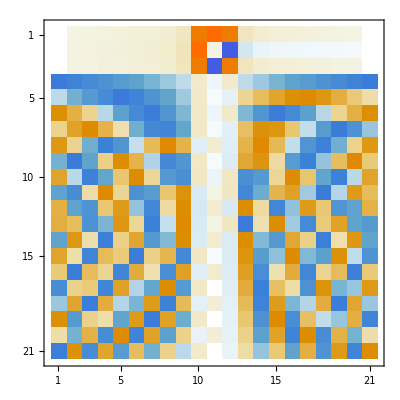

```mathematica
values//TableForm
MatrixPlot[cstates]
```

If you want to see what a particular energy eigenstate looks like in more detail, you can plot different states by changing e to an integer between 1 and n (giving the eth state above). The bar at position x in the first plot shows the coefficient of the xth basis vector. 
If we want to answer the question “where is the particle if it is in this energy eigenstate?”, then we would need to perform a position measurement. The probability that the result of this measurement is x is shown in the second plot.

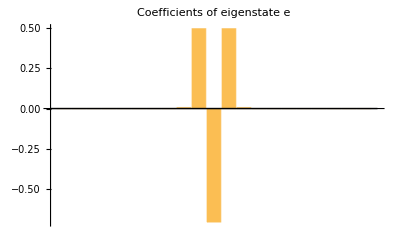

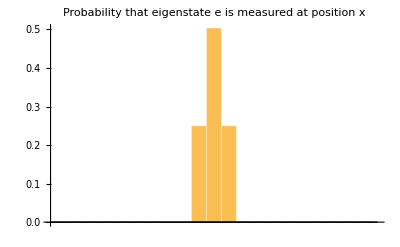

```mathematica
e=3;
BarChart[(Re[#1]&)@cstates[[e]],PlotLabel->"Coefficients of eigenstate e"]
BarChart[(Abs[#1]^2&)@cstates[[e]],PlotLabel->"Probability that eigenstate e is measured at position x"]
```

Here we view the time-evolution of particle. The graph shows the probability of measuring the particle at a given position over time, given a starting state psi0.

```mathematica
psi0[x_]:=If[x==0,1,0];

psi0vec = Table[psi0[x],{x,0,n-1}];
ergbasis = Transpose[states];
ergtime[t_]=DiagonalMatrix[(Exp[I #1 t]&)@values];
postime[t_]=ergbasis.ergtime[t].Inverse[ergbasis];
psi[t_]=postime[t].psi0vec;
psi2[t_]=(Abs[#1]^2&)@psi[t];
(*Center the state for viewing*)
cpsi2[t_]=Catenate[{psi2[t][[Ceiling[n/2]+1;;n]],psi2[t][[1;;Ceiling[n/2]]]}];
```

```mathematica
Animate[BarChart[cpsi2[tt],PlotRange->{0,1}],{tt,0,50}]
```